# xlr8r example

## Tunable Mitotic Oscillator Model of Gardner, Dolnick and Collins

References: 
(1) Gardner TS, Dolnik M, Colllins JJ (1998) "A theory for controlling cell cycle dynamics using a reversibly binding inhibitor." PNAS 95:14190-14195.
(2) Goldbeter, A. A minimal cascade model for the mitotic oscillator involving cyclin and cdc2 kinase. Proc. Natl. Acad. Sci. USA 88:9107-1101 (1991).

xlr8r implementation
created: 12-Aug-2005 BES
revised: 15-Oct-2007 BES Verify in Mathematica version 6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:04:53.252047 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

```mathematica
stn={
{∅⇄C,vi,kd},
{(C↦∅)^X, hill[1, Kd,1,0, vd]},
{MPlus↦M, hill[1, K1, 1, 0, (VM1*C[t]/(Kc+C[t]))]},
{M↦∅, hill[ 1, K2,1,0, V2]},
{XPlus↦X, hill[1, K3, 1, 0, VM3*M[t]]},
{X↦∅, hill[ 1,K4,1,0, V4]},
{∅⇄Y,VS,d1},
{C+Y⇄Z,a1,a2},
{Z->  Y, α},
{Z->  C, α}
};
```

```mathematica
interpret[stn]
```

{{C'[t]==vi-kd C[t]-(vd C[t] X[t])/(Kd+C[t])-a1 C[t] Y[t]+a2 Z[t]+α Z[t],M'[t]==-(V2 M[t])/(K2+M[t])+(VM1 C[t] MPlus[t])/((Kc+C[t]) (K1+MPlus[t])),X'[t]==-(V4 X[t])/(K4+X[t])+(VM3 M[t] XPlus[t])/(K3+XPlus[t]),Y'[t]==VS-d1 Y[t]-a1 C[t] Y[t]+a2 Z[t]+α Z[t],Z'[t]==a1 C[t] Y[t]-a2 Z[t]-2 α Z[t]},{C,M,X,Y,Z}}

```mathematica
rules={α-> 0.1, a1-> 0.5, a2-> 0.5, d1-> 0.05, VS-> 0, K1-> 0.005, K2->0.005,K3-> 0.005,K4->0.005, vi->0.025,  Kc-> 0.3,  kd-> 0.01,  VM1-> 3,  V2-> 1.5, VM3->1,  V4-> 0.5,  vd-> 0.25, Kd-> 0.02, MPlus[t]-> 1-M[t], XPlus[t]-> 1-X[t]}
```

{α→0.1,a1→0.5,a2→0.5,d1→0.05,VS→0,K1→0.005,K2→0.005,K3→0.005,K4→0.005,vi→0.025,Kc→0.3,kd→0.01,VM1→3,V2→1.5,VM3→1,V4→0.5,vd→0.25,Kd→0.02,MPlus[t]→1-M[t],XPlus[t]→1-X[t]}

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {C,M,X}

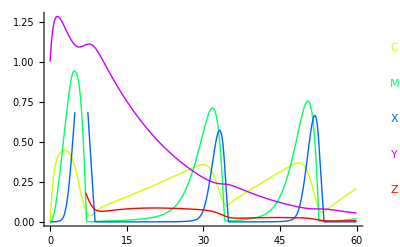

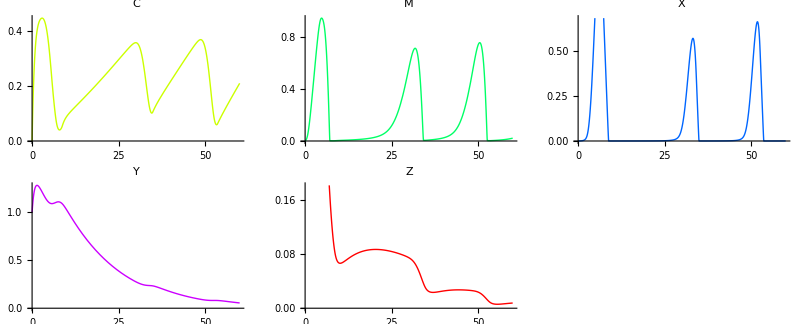

{{C→InterpolatingFunction[{{0.,60.}},<>],M→InterpolatingFunction[{{0.,60.}},<>],X→InterpolatingFunction[{{0.,60.}},<>],Y→InterpolatingFunction[{{0.,60.}},<>],Z→InterpolatingFunction[{{0.,60.}},<>]}}

```mathematica
run[stn,timeSpan-> 60,gridPlotVariables-> All, plotColumns-> 3,plot-> True,rates-> rules,initialConditions-> {Y[0]==1, Z[0]==1},MaxSteps-> 25000, ImageSize-> 800]
```